# Isotropic Source

Let a spherical source of radius R and brightness B emit radiation isotropically (i.e. specific intensity of the source integrated over all frequencies is B).

## Analytic solution

## Flux

### Flux at distance r

```mathematica
F=2Pi B  Integrate[Cos[x]Sin[x],{x,0,ArcSin[R/r]}]
```

(B π R^2)/r^2

### Flux at surface

```mathematica
F/.r->R
```

B π

## Energy density

### Energy density at distance r

```mathematica
U= 2Pi B/c Integrate[Sin[x],{x,0,ArcSin[R/r]}]
```

(2 B π (1-√(1-R^2/r^2)))/c

### Approximation for r >> R

```mathematica
UInf=Normal@Series[U/.r->1/x,{x,0,2}]/.x->1/r
```

(B π R^2)/(c r^2)

### Energy density at surface

```mathematica
{U,UInf}/.r->R
```

{(2 B π)/c,(B π)/c}

Note that using the approximation gives an incorrect answer which is off by a factor of two.

## Total energy

### Energy inside a sphere of radius r

```mathematica
e[x_]=4Pi Integrate[r^2 U,{r,R,x},Assumptions->{x>R>0,B>0,c>0}];
```

### Energy inside sphere with r = R + c t

```mathematica
e[R+c t]
```

(8 B π^2 (-R^3+(R+c t)^3-(-R^2+(R+c t)^2)^(3/2)))/(3 c)

### Comparing to power times t

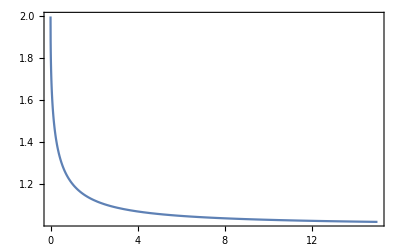

```mathematica
Plot[e[R+c t]/(F 4Pi R^2t)//.{r->R,c->1,R->1,B->1},{t,0,15},Frame->True,PlotRange->All]
```

## Special cases

## For black-body

We assume that the flux is σ T^4.

### Brightness

```mathematica
sB=Solve[F==σ T^4,B][[1,1]]
```

B→(r^2 T^4 σ)/(π R^2)

### Energy density at distance r

```mathematica
{U,UInf}/.sB
```

{(2 r^2 (1-√(1-R^2/r^2)) T^4 σ)/(c R^2),(T^4 σ)/c}

### Energy density at surface

```mathematica
{U,UInf}/.{r->R,sB}
```

{(2 r^2 T^4 σ)/(c R^2),(r^2 T^4 σ)/(c R^2)}

## From power (luminosity)

### Finding radius

```mathematica
sR=R->Solve[(4Pi R^2 F/.r->R)==P,R][[2,1,2]]
```

R→(√P)/(2 √B π)

### Finding energy density at distance r

```mathematica
{U,UInf}/.sR
```

{(2 B π (1-√(1-P/(4 B π^2 r^2))))/c,P/(4 c π r^2)}

### Value at Surface

```mathematica
{U,UInf}/.{r->R,sR}
```

{(2 B π (1-√(1-P/(4 B π^2 R^2))))/c,P/(4 c π R^2)}

## Monte Carlo simulation

## Random emission of photons

### Computing distances to photons

Here ‘ns’ is the number of photons per time-step, ‘dt’ is the length of each time-step and ‘T’ is the total time.

```mathematica
photD[ns_,dt_,T_]:=Block[{d,steps=Floor[T/dt]},d=RandomPoint[Sphere[],{2,ns steps}];
d[[2]]*=Flatten[dt Range[steps]*Partition[Sign[Total/@Times@@d],ns],1];
Norm/@Plus@@d];
```

### Counting photons in spherical shells

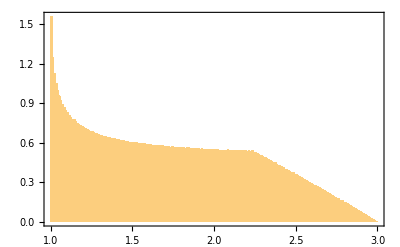

```mathematica
Histogram[photD[10^4,10^-3,2],{.01},"PDF",Frame->True]
```